```mathematica
points = {{0,0,0},{1,0,0},{1,1,0},{0,1,0},{0,0,1},{1,0,1},{1,1,1},{0,1,1}}
```

{{0,0,0},{1,0,0},{1,1,0},{0,1,0},{0,0,1},{1,0,1},{1,1,1},{0,1,1}}

```mathematica
hull =ConvexHullMesh[points]
```

-Graphics3D-

```mathematica
ConvexHullMesh[points];
Show[HighlightMesh[%,Style[2,Opacity[0.5]]],Graphics3D[Point[points]]]
```

-Graphics3D-

```mathematica
{RegionMeasure[hull],RegionCentroid[hull]} (*area and centroid*)
```

{1.,{0.5,0.5,0.5}}

```mathematica
RegionMember[hull,{0.5,0.5,0.5}]
```

True

```mathematica
RegionMember[hull,{1.5,0.5,0.5}]
```

False

```mathematica
wakePoints = {{0.5,0.5,0.5},{1.20710678,1.20710678,0.5},{1.20710678,-0.20710678,0.5},{0.5,0.5,1.5},{1.20710678,1.20710678,1.5},{1.20710678,-0.20710678,1.5}}
```

{{0.5,0.5,0.5},{1.20711,1.20711,0.5},{1.20711,-0.207107,0.5},{0.5,0.5,1.5},{1.20711,1.20711,1.5},{1.20711,-0.207107,1.5}}

```mathematica
hulltwo = ConvexHullMesh[wakePoints]
```

-Graphics3D-

```mathematica
Show[HighlightMesh[%,Style[2,Opacity[0.5]]],Graphics3D[Point[wakePoints]]]
```

-Graphics3D-

```mathematica
Show[HighlightMesh[%,Style[2,Opacity[0.5]]],Graphics3D[Point[wakePoints],Axes->{True,True,True}]]
```

HighlightMesh::meshreg: Valid MeshRegion or BoundaryMeshRegion object expected at position 1 of HighlightMesh[Show[HighlightMesh[,2],],2].

Show::gcomb: Could not combine the graphics objects in Show[HighlightMesh[Show[HighlightMesh[,2],],2],].

Show[HighlightMesh[Show[HighlightMesh[-Graphics3D-,2],-Graphics3D-],2],-Graphics3D-]

```mathematica
hulltwo
```

-Graphics3D-

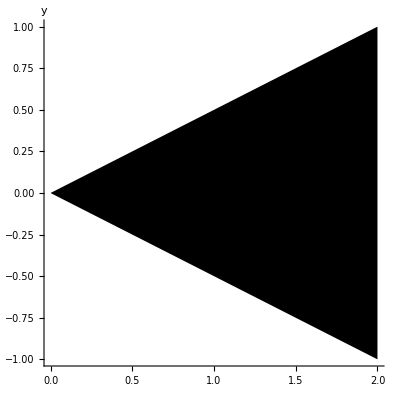

```mathematica
ConvexHullRegion[Triangle[{{0,0},{2,-1},{2,1}}],Axes->True,AxesLabel->y]
```

```mathematica
ConvexHullMesh[wakePoints, Axes->True, AxesLabel->{x,y,z}]
```

-Graphics3D-